```mathematica
SetDifference[large_,small_]:=Select[large,!MemberQ[small,#]&]
```

```mathematica
plantri8=Graph[{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5},GraphLayout->"TutteEmbedding",VertexLabels->"Name"];
```

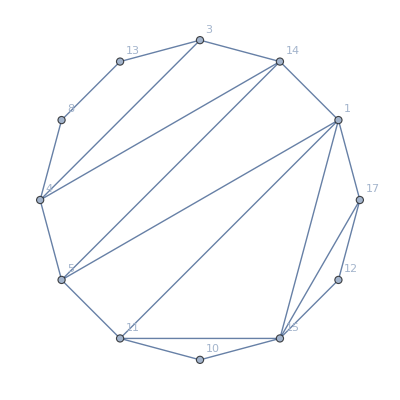

```mathematica
int=Graph[{13<->8,8<->4,4<->5,5<->11,11<->10,10<->15,15<->12,12<->17,17<->1,1<->14,3<->14,3<->13,17<->15,1<->15,11<->15,
11<->1,1<->5,
14<->5,14<->4,
4<->3},VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

```mathematica
ChromaticPolynomial[int,x]//CompleteBaseCoeff
```

{0,0,0,3,893,13321,43576,50526,25739,6370,787,46,1}

```mathematica
fint=FindFullFormula[int];
```

```mathematica
Length[fint]
```

141262

```mathematica
Select[fint,SymbolLevel[#]==4&]//Length
```

893

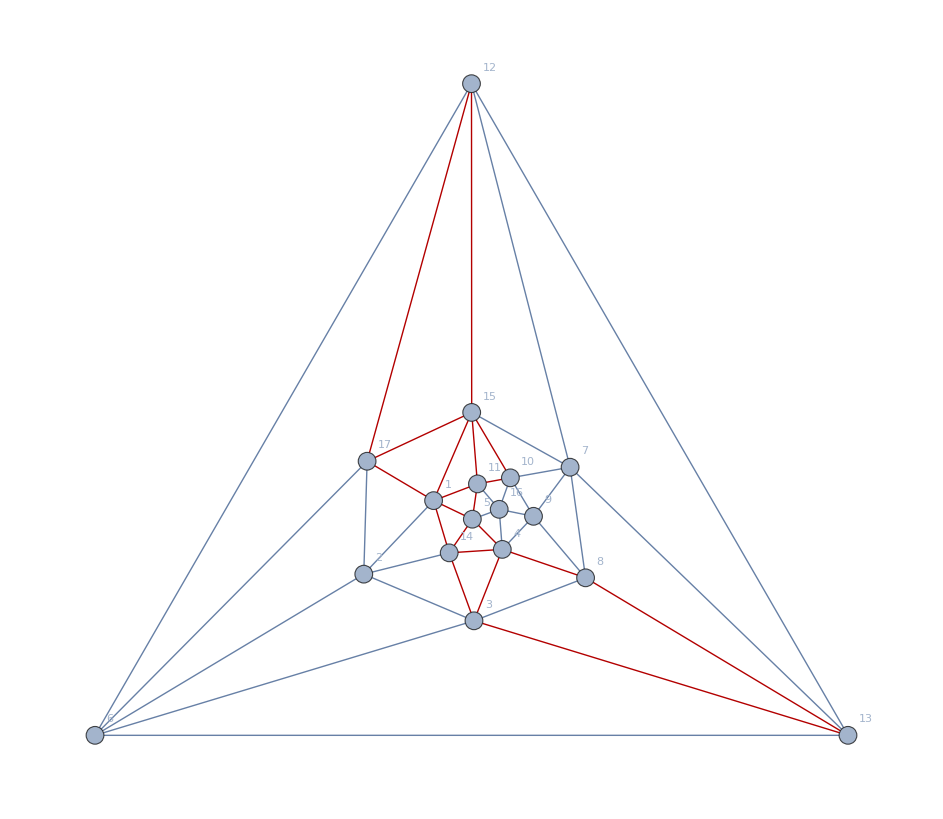

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

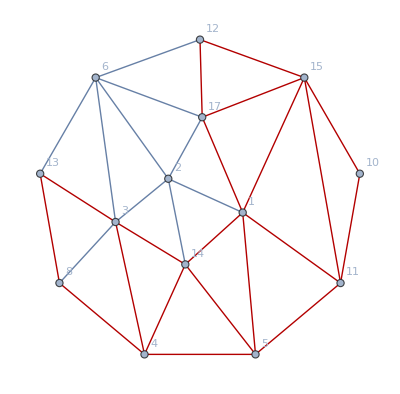

```mathematica
left=Graph[EdgeDelete[VertexDelete[plantri8,{7,9,16}],12<->13],GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

```mathematica
ChromaticPolynomial[left,x]//CompleteBaseCoeff//Total
```

2025852

```mathematica
NormalizeEdge[e]:=If[e[[1]]<e[[2]],e,UndirectedEdge[e[[2]],e[[1]]]]
```

```mathematica
SetDifference[VertexList[left],VertexList[int]]
```

{6,2}

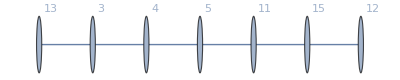

```mathematica
int
```

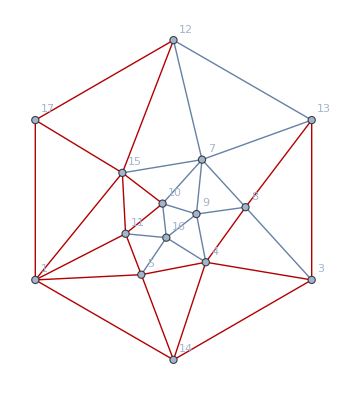

```mathematica
right=Graph[VertexDelete[plantri8,SetDifference[VertexList[left],VertexList[int]]],GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

```mathematica
ChromaticPolynomial[right,x]//CompleteBaseCoeff//Total
```

8008764

```mathematica
IsomorphicGraphQ[GraphUnion[left,right,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],plantri8]
```

True

```mathematica
IsomorphicGraphQ[GraphUnion[left,int,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],left]
```

True

```mathematica
IsomorphicGraphQ[GraphUnion[right,int,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],right]
```

True

```mathematica
crall=ChromaticPolynomial[plantri8,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13)

```mathematica
crl=ChromaticPolynomial[left,x]//Factor
```

(-3+x)^2 (-2+x)^2 (-1+x) x (2591-6660 x+7914 x^2-5645 x^3+2627 x^4-812 x^5+162 x^6-19 x^7+x^8)

```mathematica
crr=ChromaticPolynomial[right,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-289124+849630 x-1178352 x^2+1020581 x^3-613436 x^4+268200 x^5-86769 x^6+20697 x^7-3554 x^8+417 x^9-30 x^10+x^11)

```mathematica
crint=ChromaticPolynomial[int,x]//Factor
```

(-2+x)^8 (-1+x) x (3-3 x+x^2)

```mathematica
Factor[(crl*crr)]
```

(-3+x)^3 (-2+x)^3 (-1+x)^2 x^2 (2591-6660 x+7914 x^2-5645 x^3+2627 x^4-812 x^5+162 x^6-19 x^7+x^8) (-289124+849630 x-1178352 x^2+1020581 x^3-613436 x^4+268200 x^5-86769 x^6+20697 x^7-3554 x^8+417 x^9-30 x^10+x^11)

```mathematica
(Factor[(crl*crr)])/crint
```

((-3+x)^3 (-1+x) x (2591-6660 x+7914 x^2-5645 x^3+2627 x^4-812 x^5+162 x^6-19 x^7+x^8) (-289124+849630 x-1178352 x^2+1020581 x^3-613436 x^4+268200 x^5-86769 x^6+20697 x^7-3554 x^8+417 x^9-30 x^10+x^11))/((-2+x)^5 (3-3 x+x^2))